```mathematica
Factorial[365]
```

25104128675558732292929443748812027705165520269876079766872595193901106138220937419666018009000254169376172314360982328660708071123369979853445367910653872383599704355532740937678091491429440864316046925074510134847025546014098005907965541041195496105311886173373435145517193282760847755882291690213539123479186274701519396808504940722607033001246328398800550487427999876690416973437861078185344667966871511049653888130136836199010529180056125844549488648617682915826347564148990984138067809999604687488146734837340699359838791124995957584538873616661533093253551256845056046388738129702951381151861413688922986510005440943943014699244112555755279140760492764253740250410391056421979003289600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
P[n_]:=Factorial[365]/Factorial[365-n]/(365)^n
```

```mathematica
N[P[23]]
```

0.492703

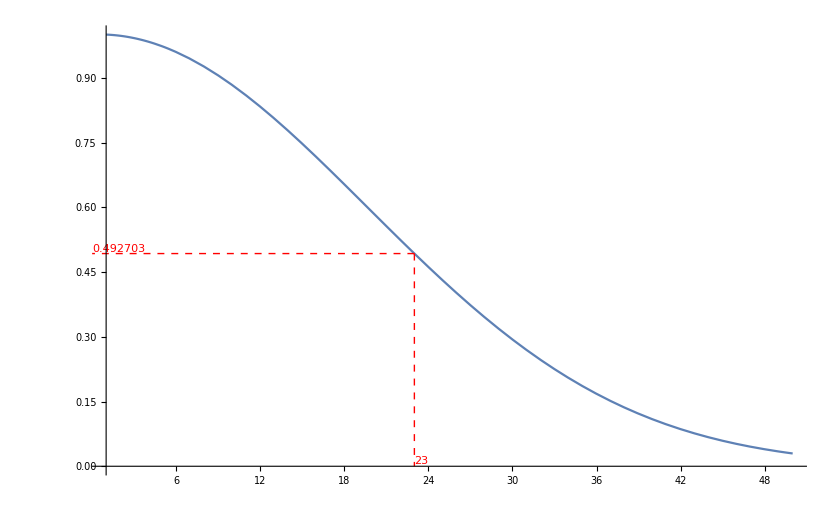

```mathematica
Plot[P[x],{x,1,50},Epilog->{Red,Dashed,Line[{{23,P[23]},{23,0}}],Red,Dashed,Line[{{23,P[23]},{0,P[23]}}],Text[N[P[23]],{0,N[P[23]]},{-2,-1}],Text[23,{23,0},{-2,-1}]}]
```

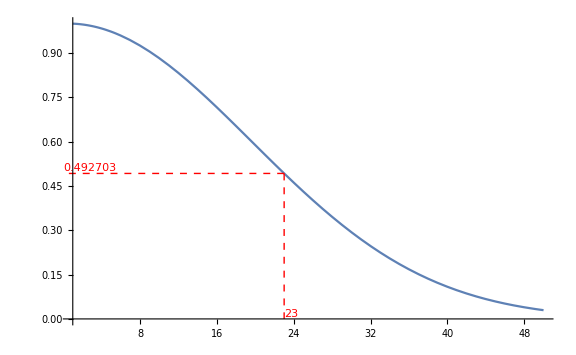

```mathematica
Show[%16,ImageSize->Large]
```

```mathematica
man=Manipulate[Plot[P[x],{x,1,100},ImageSize->{700,450},Epilog->{Red,Dashed,Line[{{n,P[n]},{n,0}}],Red,Dashed,Line[{{n,P[n]},{0,P[n]}}],Text[N[P[n]],{0,N[P[n]]},{-2,-1}],Text[n,{n,0},{-2,-1}]}],{n,1,50,1,Appearance->"Open"},ContentSize->750]
```

```mathematica
Export["Birthday.gif",man]
```

Birthday.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Birthday.gif"]]]
```